# Staggered chemical potential and the surface bands of Sr_2 RuO_4

Anirudh Chandrasekaran

Loughborough University
14 June 2024

In this notebook we will examine the effect of a staggered chemical potential on the dispersion of the surface bands of Sr_2 RuO_4. We will focus in particular on the M point. The staggered chemical potential breaks the lattice reflection symmetry but preserves the fourfold rotation symmetry about each Ru atom. As we will see below, this allows the two d_xy bands at the M point to decouple and become individually four-fold symmetric. This allows the bands to host X_9 singularities under tuning.

## Loading the Library

We first load the library by executing the following:

```mathematica
AppendTo[$Path,StringDelete[NotebookDirectory[],"/Sr2RuO4"]<>"Package"];
<<BandUtilities`
```

## Interpolating between the Wannier90 files

### Ingredients needed for symmetrization

```mathematica
ρ={{0,-1,0},{1,0,0},{0,0,1}}; (*The matrix part of the Subscript[C, 4] rotation about one of the Ru atoms.*)
Uρ={{0,-1,0},{1,0,0},{0,0,-1}}; (*Representation of Subscript[C, 4] rotation in the d-orbital space.*)

rxy={{0,1,0},{1,0,0},{0,0,1}};  (*x<->y reflection.*)
Urxy={{-1,0,0},{0,1,0},{0,0,-1}}; (*Representation of the x<->y reflection.*)

c0={1/4,3/4,0}; (*Location of one of the Ru atoms, which we shall use as the centre of the Subscript[C, 4] rotation.*)

AtomLocations={{3/4,1/4,0},{3/4,1/4,0},{3/4,1/4,0},{1/4,3/4,0},{1/4,3/4,0},{1/4,3/4,0}}; (*Location of the basis atoms in the fractional coordinates within the unit cell.*)

SymmetryList={}; (*This is a multidimensional list which we shall construct below. Each element is a sublist corresponding to a particular symmetry. First element of the sublist is real space symmetry's matrix part, second element is the translation part and the third element is its representation in the Hilbert space. Our point group is Subscript[D, 4], or Subscript[D, 8] in some pepole's notation.*)
Do[
AppendTo[SymmetryList,{MatrixPower[ρ,i],(c0-MatrixPower[ρ,i].c0)//Simplify,ArrayFlatten[IdentityMatrix[2]⊗MatrixPower[Uρ,i]]}];

AppendTo[SymmetryList,{MatrixPower[ρ,i].rxy,(c0-MatrixPower[ρ,i].c0)//Simplify,ArrayFlatten[IdentityMatrix[2]⊗MatrixPower[Uρ,i]].ArrayFlatten[{{0,1},{1,0}}⊗Urxy]}];
,{i,1,4}];
```

### Interpolation with symmetrization

We now interpolate between the Wannier90 data for 13 different rotations of the RuO octahedra: 0° through 12° to generate a continuously θ dependent Hamiltonian, whilst ensuring that the interpolated model has the right symmetry (for which we are feeding the list SymmetryList):

```mathematica
FileLocn=NotebookDirectory[]<>"unrenormalized2/";

W90Data=LoadInterpolateTBMs[{FileLocn<>"Sr2RuO4_0deg.dat",FileLocn<>"Sr2RuO4_1deg.dat",FileLocn<>"Sr2RuO4_2deg.dat",FileLocn<>"Sr2RuO4_3deg.dat",FileLocn<>"Sr2RuO4_4deg.dat",FileLocn<>"Sr2RuO4_5deg.dat",FileLocn<>"Sr2RuO4_6deg.dat",FileLocn<>"Sr2RuO4_7deg.dat",FileLocn<>"Sr2RuO4_8deg.dat",FileLocn<>"Sr2RuO4_9deg.dat",FileLocn<>"Sr2RuO4_10deg.dat",FileLocn<>"Sr2RuO4_11deg.dat",FileLocn<>"Sr2RuO4_12deg.dat"},{0,1,2,3,4,5,6,7,8,9,10,11,12},"Symmetries"->SymmetryList,"OrbitalCentres"->AtomLocations,"ParameterSymbol"->"θ"];
```

Invalid or no lattice vectors provided! Using unit vectors.

Tight-binding data files loaded.

Space dimension: 3

Number of orbitals: 6

Number of supercells: 49

Number of models/data-files to interpolate: 13

Number of lines in the data files: {741,853,853,853,845,853,853,853,853,853,853,853,853}

Interpolating between the Hamiltonians.

Valid symmetrization scheme provided! We will symmetrize the loaded Hamiltonian.

Number of supercells after symmetrization: 79

Since this is largely an exploratory analysis, we will not include the overall band renormalization or the spin orbit term which have minimal impact on the M point. We begin by adding a staggered chemical potential Δ

```mathematica
Hamltn1[k1_,k2_,θ_,Δ_]=W90Data[[1]]+DiagonalMatrix[{Δ,Δ,Δ,-Δ,-Δ,-Δ}];
```

## Tuning to a HOS with non - zero Δ

We begin by defining a version of the Hamiltonian suitable for series expansion (once again in the bulk Brillouin zone basis for the sake of consistency)

```mathematica
Ham[k_]:=Hamltn1[k[[1]]-k[[2]],k[[1]]+k[[2]],k[[3]],k[[4]]]
```

To compute the Hessian determinant with δθ and δΔ corrections, we need to series expand the dispersion to quadratic order with corrections. To find the bands closest to Fermi level to series expand, we first calculate the eigenvalues at the M point for a small Δ=0.005 (that is 5 meV).

```mathematica
Sort[Eigenvalues[Ham[{0,π//N,8,0.005}]]]
```

{-0.555813,-0.555813,-0.076319,-0.066319,0.286847,0.286847}

It is clear that bands 3 and 4 are the bands of interest closest to the Fermi level. We will plot these bands with orbital projection once the critical θ has been figured out.

### Band 3

```mathematica
TaylA=Chop[TaylorExpandBand[Ham,{0,π//N,8,0.005},3,2,"Dimension"->2,"TuningDegree"->2,"TuningSymbol"->{"δθ","δΔ"},"Messages"->False][[1]],10^-8];
```

```mathematica
Chop[Total[TaylA]]/.{p1->Subscript[k, x],p2->Subscript[k, y]}
```

-0.076319-1. δΔ+(-0.0205955+0.00119685 δθ) δθ+(-0.014985+8.34065×10^-8 δΔ^2+(0.0320869-0.000243806 δθ) δθ) k_x^2+(-0.014985-8.34065×10^-8 δΔ^2+(0.0320869-0.000243806 δθ) δθ) k_y^2

We note that the quadratic term contains a very small δΔ correction. This indicates that the critical θ does not depend strongly on Δ (as long as it is non-zero and small. For large Δ, this analysis based on series expansion to quadratic order may not hold).

We can compute the Hessian determinant and solve for δθ by setting it to zero:

```mathematica
HesDet=((D[TaylA[[3]],{p1,2}]D[TaylA[[3]],{p2,2}])-(D[TaylA[[3]],p1,p2])^2)/.{p1->0,p2->0,δλ->0,δΔ->0}//Simplify
Soln1=Solve[HesDet==0,δθ]
```

0.000898201-0.00384658 δθ+0.00414751 δθ^2-0.000062584 δθ^3+2.37766×10^-7 δθ^4

{{δθ→0.468682},{δθ→0.468682},{δθ→131.14},{δθ→131.14}}

The critical θ to the first approximation is then given by

```mathematica
TaylB=Chop[TaylorExpandBand[Ham,{0,π//N,8+δθ/.Soln1[[1]],0.005},3,2,"Dimension"->2,"TuningDegree"->2,"TuningSymbol"->{"δθ","δΔ"},"Messages"->False][[1]],10^-8];
```

```mathematica
Total[TaylB]/.{p1->Subscript[k, x],p2->Subscript[k, y]}
```

-0.0856538-1. δΔ+(-0.0191726+0.00162093 δθ) δθ+(0.0000166482-3.94981×10^-8 δΔ^2+(0.0319471-0.000137449 δθ) δθ) k_x^2+(0.0000166482+3.94981×10^-8 δΔ^2+(0.0319471-0.000137449 δθ) δθ) k_y^2

Indeed the coefficients of the quadratic terms have become quite small. We can repeat the process once again to obtain better convergence

```mathematica
HesDet=((D[TaylB[[3]],{p1,2}]D[TaylB[[3]],{p2,2}])-(D[TaylB[[3]],p1,p2])^2)/.{p1->0,p2->0,δλ->0,δΔ->0}//Simplify
Soln2=Solve[HesDet==0,δθ]
```

1.10864×10^-9+4.25488×10^-6 δθ+0.00408246 δθ^2-0.0000351289 δθ^3+7.55692×10^-8 δθ^4

{{δθ→-0.000521115},{δθ→-0.000521115},{δθ→232.429},{δθ→232.429}}

Thus, the critical theta is given by

```mathematica
θcrit=8+(δθ/.Soln1[[1]])+(δθ/.Soln2[[1]])
```

8.46816

Using this, we go ahead and define the Hamiltonian at the critical θ:

```mathematica
HamCrit[k_]:=Hamltn1[k[[1]]-k[[2]],k[[1]]+k[[2]],θcrit,0.005]
```

```mathematica
TaylC=Chop[TaylorExpandBand[HamCrit,{0,π//N},3,4,"Messages"->False][[1]],10^-8];
```

```mathematica
Total[TaylC]/.{p1->Subscript[k, x],p2->Subscript[k, y]}
```

-0.0856438-0.630949 k_x^4+0.102619 k_x^3 k_y+0.860439 k_x^2 k_y^2-0.102619 k_x k_y^3-0.630949 k_y^4

This is obviously a singularity belonging to the X_9 class. We can confirm this explicitly

```mathematica
DiagnoseHOS[Total[TaylC]/.{p1->Subscript[k, x],p2->Subscript[k, y]}]
```

Polynomial has corank 2. It is 5-determinate. Its determinacy is either 5 or 4 and its codimension is 8. Comparing with the known list of singularities:

Polynomial has a catastrophe belonging to the X_9 singularity class.

{2,8,5}

We can also explicitly check that this satisfies the four fold rotation symmetry (k_x,k_y)->(k_y,-k_x) but not the mirror symmetry (k_x,k_y)->(k_y,k_x) since the latter is broken while the former is preserved under the staggered chemical potential Δ.

```mathematica
Chop[((TaylC/.{p1->Subscript[k, x],p2->Subscript[k, y]})-(TaylC/.{p1->Subscript[k, y],p2->-Subscript[k, x]}))//FullSimplify,10^-6]//Total
Chop[((TaylC/.{p1->Subscript[k, x],p2->Subscript[k, y]})-(TaylC/.{p1->Subscript[k, y],p2->Subscript[k, x]}))//FullSimplify,10^-6]//Total
```

0

0.205239 k_x^3 k_y-0.205239 k_x k_y^3

The 3D and surface plot of the dispersion

```mathematica
Plot3D[Total[TaylC],{p1,-1/4,1/4},{p2,-1/4,1/4}]
```

-Graphics3D-

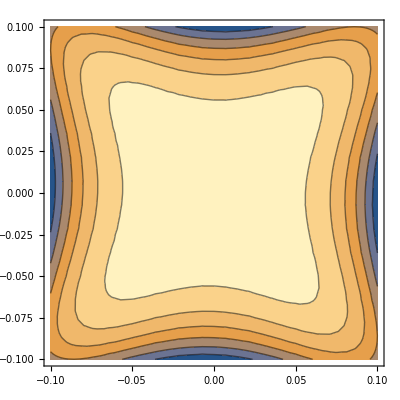

```mathematica
ContourPlot[Total[TaylC],{p1,-1/10,1/10},{p2,-1/10,1/10}]
```

These indicate that this is a four fold maximum rather than a saddle.

### Band 4

```mathematica
TaylA2=Chop[TaylorExpandBand[Ham,{0,π//N,8,0.005},4,2,"Dimension"->2,"TuningDegree"->2,"TuningSymbol"->{"δθ","δΔ"},"Messages"->False][[1]],10^-8];
```

```mathematica
Total[TaylA2]/.{p1->Subscript[k, x],p2->Subscript[k, y]}
```

-0.066319+1. δΔ+(-0.0205955+0.00119685 δθ) δθ+(-0.014985-8.34065×10^-8 δΔ^2+(0.0320869-0.000243806 δθ) δθ) k_x^2+(-0.014985+8.34065×10^-8 δΔ^2+(0.0320869-0.000243806 δθ) δθ) k_y^2

We note that the quadratic term contains a very small δΔ correction. This indicates that the critical θ does not depend strongly on Δ (as long as it is non-zero and small. For large Δ, this analysis based on series expansion to quadratic order may not hold).

We can compute the Hessian determinant and solve for δθ by setting it to zero:

```mathematica
HesDet=((D[TaylA2[[3]],{p1,2}]D[TaylA2[[3]],{p2,2}])-(D[TaylA2[[3]],p1,p2])^2)/.{p1->0,p2->0,δλ->0,δΔ->0}//Simplify
Soln12=Solve[HesDet==0,δθ]
```

0.000898201-0.00384658 δθ+0.00414751 δθ^2-0.000062584 δθ^3+2.37766×10^-7 δθ^4

{{δθ→0.468682},{δθ→0.468682},{δθ→131.14},{δθ→131.14}}

The critical θ to the first approximation is then given by

```mathematica
TaylB2=Chop[TaylorExpandBand[Ham,{0,π//N,8+δθ/.Soln12[[1]],0.005},4,2,"Dimension"->2,"TuningDegree"->2,"TuningSymbol"->{"δθ","δΔ"},"Messages"->False][[1]],10^-8];
```

```mathematica
Total[TaylB2]/.{p1->Subscript[k, x],p2->Subscript[k, y]}
```

-0.0756538+1. δΔ+(-0.0191726+0.00162093 δθ) δθ+(0.0000166482-9.02946×10^-8 δΔ^2+(0.0319471-0.000137449 δθ) δθ) k_x^2+(0.0000166482+9.02946×10^-8 δΔ^2+(0.0319471-0.000137449 δθ) δθ) k_y^2

Indeed the coefficients of the quadratic terms have become quite small. We can repeat the process once again to obtain better convergence

```mathematica
HesDet=((D[TaylB2[[3]],{p1,2}]D[TaylB2[[3]],{p2,2}])-(D[TaylB2[[3]],p1,p2])^2)/.{p1->0,p2->0,δλ->0,δΔ->0}//Simplify
Soln22=Solve[HesDet==0,δθ]
```

1.10864×10^-9+4.25488×10^-6 δθ+0.00408246 δθ^2-0.0000351289 δθ^3+7.55692×10^-8 δθ^4

{{δθ→-0.000521115},{δθ→-0.000521115},{δθ→232.429},{δθ→232.429}}

Thus, the critical theta is given by

```mathematica
θcrit2=8+(δθ/.Soln12[[1]])+(δθ/.Soln22[[1]])
```

8.46816

Using this, we go ahead and define the Hamiltonian at the critical θ:

```mathematica
HamCrit2[k_]:=Hamltn1[k[[1]]-k[[2]],k[[1]]+k[[2]],θcrit2,0.005]
```

```mathematica
TaylC2=Chop[TaylorExpandBand[HamCrit2,{0,π//N},4,4,"Messages"->False][[1]],10^-8];
```

```mathematica
Total[TaylC2]/.{p1->Subscript[k, x],p2->Subscript[k, y]}
```

-0.0756438+0.201354 k_x^4-0.102619 k_x^3 k_y-0.804168 k_x^2 k_y^2+0.102619 k_x k_y^3+0.201354 k_y^4

This is obviously a singularity belonging to the X_9 class. We can confirm this explicitly

```mathematica
DiagnoseHOS[Total[TaylC2]/.{p1->Subscript[k, x],p2->Subscript[k, y]}]
```

Polynomial has corank 2. It is 5-determinate. Its determinacy is either 5 or 4 and its codimension is 8. Comparing with the known list of singularities:

Polynomial has a catastrophe belonging to the X_9 singularity class.

{2,8,5}

We can also explicitly check that this satisfies the four fold rotation symmetry (k_x,k_y)->(k_y,-k_x) but not the mirror symmetry (k_x,k_y)->(k_y,k_x) since the latter is broken while the former is preserved under the staggered chemical potential Δ.

```mathematica
Chop[((TaylC2/.{p1->Subscript[k, x],p2->Subscript[k, y]})-(TaylC2/.{p1->Subscript[k, y],p2->-Subscript[k, x]}))//FullSimplify,10^-6]//Total
Chop[((TaylC2/.{p1->Subscript[k, x],p2->Subscript[k, y]})-(TaylC2/.{p1->Subscript[k, y],p2->Subscript[k, x]}))//FullSimplify,10^-6]//Total
```

0

-0.205239 k_x^3 k_y+0.205239 k_x k_y^3

The 3D and surface plot of the dispersion

```mathematica
Plot3D[Total[TaylC2],{p1,-1/4,1/4},{p2,-1/4,1/4}]
```

-Graphics3D-

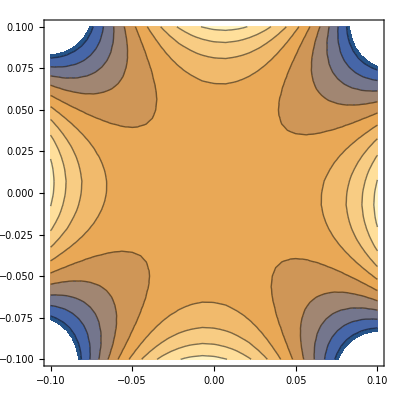

```mathematica
ContourPlot[Total[TaylC2],{p1,-1/10,1/10},{p2,-1/10,1/10}]
```

These confirm that this is a genuine four fold saddle.

### Comparing bands 3 and 4

We can finally compare the HOS in band 3 and band 4 (recall that these bands were degenerate before the staggered chemical potential was applied)

```mathematica
Total[TaylC]/.{p1->Subscript[k, x],p2->Subscript[k, y]}
Total[TaylC2]/.{p1->Subscript[k, x],p2->Subscript[k, y]}
```

-0.0856438-0.630949 k_x^4+0.102619 k_x^3 k_y+0.860439 k_x^2 k_y^2-0.102619 k_x k_y^3-0.630949 k_y^4

-0.0756438+0.201354 k_x^4-0.102619 k_x^3 k_y-0.804168 k_x^2 k_y^2+0.102619 k_x k_y^3+0.201354 k_y^4

It is clear that while band 3 (with negative k_x^4 and k_y^4 terms) and band 4 (with positive k_x^4 and k_y^4 terms) disperse roughly in the opposite fashion. This is obviously an approximate qualification since the k_x^2 k_y^2 terms also play a role. We now plot the band structure with orbital projections

```mathematica
δk=3.869  0.35;
HSymmPts={{{-δk,π-δk},"← -(M̄)_1"},{{0,π},"(M̄)_2"},{{0,π+δk+0.01},"Γ →"}};
Bnds=GenerateBandStructure[HamCrit,HSymmPts,"OrbitalProjection"->True,"OrbitalGrouping"->{{1,4},{2,5},{3,6}},"TotalPoints"->400];
```

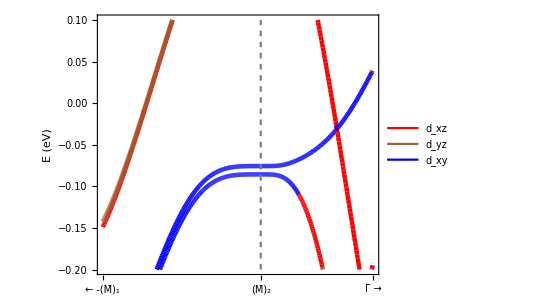

```mathematica
PlotBandStructure[Bnds,(*{-0.042,0.012}*){-0.2,0.1},AspectRatio->3/4,"yLabel"->{(*Label*)"E (eV)",(*Font Size*)13,(*Font Color*)Black,(*Font Family*)"Arial"},"xLabel"->{13,Black,"Arial"},"yTicks"->{12,Black,"Helvetica"},"LineThickness"->0.008,"LineColorScheme"->{Red,Brown,Blue},(*Dividing Lines*)"DividingLines"->{(*Dashing[..]*)0.01,(*Color*)Gray,(*Thickness*)0.004},(*,Legend*)"PlotKeyLegend"->{{"d_xz","d_yz","d_xy"},{0.25,0.85}}]
```

We notice that the M point singularities arise primarily from the d_xy orbitals. Further the higher order saddle nature of band 4 and the higher order maximum nature of band 3 are quite apparent.

## Evolution of the critical point

### Band 3

```mathematica
Do[
Print["Δ_stag = ",Round[1000Delt],"meV"];

Do[

HamCurr[k_]:=Hamltn1[k[[1]]-k[[2]],k[[1]]+k[[2]],θCurr,Delt];


TaylorPoly=Chop[Total[TaylorExpandBand[HamCurr,{0,π//N},3,2,"Messages"->False][[1]]],10^-5];

HesDet=(D[TaylorPoly,{p1,2}]D[TaylorPoly,{p2,2}]-(D[TaylorPoly,p1,p2])^2)/.{p1->0,p2->0}//Simplify;

Print["\t","θ = ",θCurr,", Tayl = ",Chop[NumberForm[TaylorPoly,{4,3}]/.{p1->Subscript[k, x],p2->Subscript[k, y]},10^-3]];


,{θCurr,7,12,1}];

,{Delt,0.001,0.008,0.001}];
```

Δ_stag = 1meV

θ = 7, Tayl = -0.052-0.048 k_x^2-0.048 k_y^2

θ = 8, Tayl = -0.072-0.015 k_x^2-0.015 k_y^2

θ = 9, Tayl = -0.091+0.017 k_x^2+0.017 k_y^2

θ = 10, Tayl = -0.109+0.047 k_x^2+0.047 k_y^2

θ = 11, Tayl = -0.137+0.075 k_x^2+0.075 k_y^2

θ = 12, Tayl = -0.149+0.096 k_x^2+0.096 k_y^2

Δ_stag = 2meV

θ = 7, Tayl = -0.053-0.048 k_x^2-0.048 k_y^2

θ = 8, Tayl = -0.073-0.015 k_x^2-0.015 k_y^2

θ = 9, Tayl = -0.092+0.017 k_x^2+0.017 k_y^2

θ = 10, Tayl = -0.110+0.047 k_x^2+0.047 k_y^2

θ = 11, Tayl = -0.138+0.075 k_x^2+0.075 k_y^2

θ = 12, Tayl = -0.150+0.096 k_x^2+0.096 k_y^2

Δ_stag = 3meV

θ = 7, Tayl = -0.054-0.048 k_x^2-0.048 k_y^2

θ = 8, Tayl = -0.074-0.015 k_x^2-0.015 k_y^2

θ = 9, Tayl = -0.093+0.017 k_x^2+0.017 k_y^2

θ = 10, Tayl = -0.111+0.047 k_x^2+0.047 k_y^2

θ = 11, Tayl = -0.139+0.075 k_x^2+0.075 k_y^2

θ = 12, Tayl = -0.151+0.096 k_x^2+0.096 k_y^2

Δ_stag = 4meV

θ = 7, Tayl = -0.055-0.048 k_x^2-0.048 k_y^2

θ = 8, Tayl = -0.075-0.015 k_x^2-0.015 k_y^2

θ = 9, Tayl = -0.094+0.017 k_x^2+0.017 k_y^2

θ = 10, Tayl = -0.112+0.047 k_x^2+0.047 k_y^2

θ = 11, Tayl = -0.140+0.075 k_x^2+0.075 k_y^2

θ = 12, Tayl = -0.152+0.096 k_x^2+0.096 k_y^2

Δ_stag = 5meV

θ = 7, Tayl = -0.056-0.048 k_x^2-0.048 k_y^2

θ = 8, Tayl = -0.076-0.015 k_x^2-0.015 k_y^2

θ = 9, Tayl = -0.095+0.017 k_x^2+0.017 k_y^2

θ = 10, Tayl = -0.113+0.047 k_x^2+0.047 k_y^2

θ = 11, Tayl = -0.141+0.075 k_x^2+0.075 k_y^2

θ = 12, Tayl = -0.153+0.096 k_x^2+0.096 k_y^2

Δ_stag = 6meV

θ = 7, Tayl = -0.057-0.048 k_x^2-0.048 k_y^2

θ = 8, Tayl = -0.077-0.015 k_x^2-0.015 k_y^2

θ = 9, Tayl = -0.096+0.017 k_x^2+0.017 k_y^2

θ = 10, Tayl = -0.114+0.047 k_x^2+0.047 k_y^2

θ = 11, Tayl = -0.142+0.075 k_x^2+0.075 k_y^2

θ = 12, Tayl = -0.154+0.096 k_x^2+0.096 k_y^2

Δ_stag = 7meV

θ = 7, Tayl = -0.058-0.048 k_x^2-0.048 k_y^2

θ = 8, Tayl = -0.078-0.015 k_x^2-0.015 k_y^2

θ = 9, Tayl = -0.097+0.017 k_x^2+0.017 k_y^2

θ = 10, Tayl = -0.115+0.047 k_x^2+0.047 k_y^2

θ = 11, Tayl = -0.143+0.075 k_x^2+0.075 k_y^2

θ = 12, Tayl = -0.155+0.096 k_x^2+0.096 k_y^2

Δ_stag = 8meV

θ = 7, Tayl = -0.059-0.048 k_x^2-0.048 k_y^2

θ = 8, Tayl = -0.079-0.015 k_x^2-0.015 k_y^2

θ = 9, Tayl = -0.098+0.017 k_x^2+0.017 k_y^2

θ = 10, Tayl = -0.116+0.047 k_x^2+0.047 k_y^2

θ = 11, Tayl = -0.144+0.075 k_x^2+0.075 k_y^2

θ = 12, Tayl = -0.156+0.096 k_x^2+0.096 k_y^2

It is clear from the signs of the k_x^2 and k_y^2 coefficients that the VHS simply transitions from an ordinary maximum to ordinary minimum (somewhere between 8° and 9°). We will find the precise location of the HOVHS below.

### Band 4

```mathematica
Do[
Print["Δ_stag = ",Round[1000Delt],"meV"];

Do[

HamCurr[k_]:=Hamltn1[k[[1]]-k[[2]],k[[1]]+k[[2]],θCurr,Delt];


TaylorPoly=Chop[Total[TaylorExpandBand[HamCurr,{0,π//N},4,2,"Messages"->False][[1]]],10^-5];

HesDet=(D[TaylorPoly,{p1,2}]D[TaylorPoly,{p2,2}]-(D[TaylorPoly,p1,p2])^2)/.{p1->0,p2->0}//Simplify;

Print["\t","θ = ",θCurr,", Tayl = ",Chop[NumberForm[TaylorPoly,{4,3}]/.{p1->Subscript[k, x],p2->Subscript[k, y]},10^-3]];


,{θCurr,7,12,1}];

,{Delt,0.001,0.008,0.001}];
```

Δ_stag = 1meV

θ = 7, Tayl = -0.050-0.048 k_x^2-0.048 k_y^2

θ = 8, Tayl = -0.070-0.015 k_x^2-0.015 k_y^2

θ = 9, Tayl = -0.089+0.017 k_x^2+0.017 k_y^2

θ = 10, Tayl = -0.107+0.047 k_x^2+0.047 k_y^2

θ = 11, Tayl = -0.135+0.075 k_x^2+0.075 k_y^2

θ = 12, Tayl = -0.147+0.096 k_x^2+0.096 k_y^2

Δ_stag = 2meV

θ = 7, Tayl = -0.049-0.048 k_x^2-0.048 k_y^2

θ = 8, Tayl = -0.069-0.015 k_x^2-0.015 k_y^2

θ = 9, Tayl = -0.088+0.017 k_x^2+0.017 k_y^2

θ = 10, Tayl = -0.106+0.047 k_x^2+0.047 k_y^2

θ = 11, Tayl = -0.134+0.075 k_x^2+0.075 k_y^2

θ = 12, Tayl = -0.146+0.096 k_x^2+0.096 k_y^2

Δ_stag = 3meV

θ = 7, Tayl = -0.048-0.048 k_x^2-0.048 k_y^2

θ = 8, Tayl = -0.068-0.015 k_x^2-0.015 k_y^2

θ = 9, Tayl = -0.087+0.017 k_x^2+0.017 k_y^2

θ = 10, Tayl = -0.105+0.047 k_x^2+0.047 k_y^2

θ = 11, Tayl = -0.133+0.075 k_x^2+0.075 k_y^2

θ = 12, Tayl = -0.145+0.096 k_x^2+0.096 k_y^2

Δ_stag = 4meV

θ = 7, Tayl = -0.047-0.048 k_x^2-0.048 k_y^2

θ = 8, Tayl = -0.067-0.015 k_x^2-0.015 k_y^2

θ = 9, Tayl = -0.086+0.017 k_x^2+0.017 k_y^2

θ = 10, Tayl = -0.104+0.047 k_x^2+0.047 k_y^2

θ = 11, Tayl = -0.132+0.075 k_x^2+0.075 k_y^2

θ = 12, Tayl = -0.144+0.096 k_x^2+0.096 k_y^2

Δ_stag = 5meV

θ = 7, Tayl = -0.046-0.048 k_x^2-0.048 k_y^2

θ = 8, Tayl = -0.066-0.015 k_x^2-0.015 k_y^2

θ = 9, Tayl = -0.085+0.017 k_x^2+0.017 k_y^2

θ = 10, Tayl = -0.103+0.047 k_x^2+0.047 k_y^2

θ = 11, Tayl = -0.131+0.075 k_x^2+0.075 k_y^2

θ = 12, Tayl = -0.143+0.096 k_x^2+0.096 k_y^2

Δ_stag = 6meV

θ = 7, Tayl = -0.045-0.048 k_x^2-0.048 k_y^2

θ = 8, Tayl = -0.065-0.015 k_x^2-0.015 k_y^2

θ = 9, Tayl = -0.084+0.017 k_x^2+0.017 k_y^2

θ = 10, Tayl = -0.102+0.047 k_x^2+0.047 k_y^2

θ = 11, Tayl = -0.130+0.075 k_x^2+0.075 k_y^2

θ = 12, Tayl = -0.142+0.096 k_x^2+0.096 k_y^2

Δ_stag = 7meV

θ = 7, Tayl = -0.044-0.048 k_x^2-0.048 k_y^2

θ = 8, Tayl = -0.064-0.015 k_x^2-0.015 k_y^2

θ = 9, Tayl = -0.083+0.017 k_x^2+0.017 k_y^2

θ = 10, Tayl = -0.101+0.047 k_x^2+0.047 k_y^2

θ = 11, Tayl = -0.129+0.075 k_x^2+0.075 k_y^2

θ = 12, Tayl = -0.141+0.096 k_x^2+0.096 k_y^2

Δ_stag = 8meV

θ = 7, Tayl = -0.043-0.048 k_x^2-0.048 k_y^2

θ = 8, Tayl = -0.063-0.015 k_x^2-0.015 k_y^2

θ = 9, Tayl = -0.082+0.017 k_x^2+0.017 k_y^2

θ = 10, Tayl = -0.100+0.047 k_x^2+0.047 k_y^2

θ = 11, Tayl = -0.128+0.075 k_x^2+0.075 k_y^2

θ = 12, Tayl = -0.140+0.096 k_x^2+0.096 k_y^2

Here as well, the VHS simply transitions from an ordinary maximum to ordinary minimum (somewhere between 8° and 9°). We will find the precise location of the HOVHS below.

Thus we see that both the singularities transition from an ordinary maximum to an ordinary minimum probably through a HOVHS somewhere between 8° and 9°. This is not surprising since Δ_stag does not break the four fold rotation at the M point, so an ordinary saddle is prohibited when the bands are decoupled.

## Nature of the HOS

### Band 3

```mathematica
HosListBand3M={};
SetSharedVariable[HosListBand3M];

ParallelDo[
HamCurr[k_]:=Hamltn1[k[[1]]-k[[2]],k[[1]]+k[[2]],k[[3]],Delt];

θCurr=8.46;
CurrResln=10^-3;
HOSFound=False;
NoTry=1;

While[NoTry<=4&&HOSFound==False,
TaylorPoly=Chop[TaylorExpandBand[HamCurr(*The Hamiltonian*),{0,π//N,θCurr}(*the (k,t) point at which we are going to series expand.*),3(*Band to series expand*),2(*Degree of Taylor polynomial*),"Dimension"->2(*k-space dimension*),"TuningDegree"->2(*Degree of tuning parameter terms*),"TuningSymbol"->"δθ"(*Symbols for the tuning parameters*),"Resolution"->10^-4(*Resolution below which we shall kill terms*),"SampleDirection"->{0.333,0.779,0.1335}(*A sample k-vector that will be used for diagonalising symbolic matrices. This is not needed in principle since we will generate a random one in the routine if this is not provided*),"Messages"->False(*YesMessage*)],10^-6];

HesDet=(D[TaylorPoly[[1,3]],{p1,2}]D[TaylorPoly[[1,3]],{p2,2}]-(D[TaylorPoly[[1,3]],p1,p2])^2)/.{p1->0,p2->0}//Simplify;

If[Chop[ReplaceAll[HesDet,{δθ->0}],CurrResln]==0,
HOSFound=True;
];

δθSolns=Solve[HesDet==0,δθ,Reals];

MinSoln=1;
Do[
If[Abs[ReplaceAll[δθ,δθSolns[[l]]]]<Abs[ReplaceAll[δθ,δθSolns[[MinSoln]]]],
MinSoln=l;
]
,{l,1,Length[δθSolns]}];

θCurr=θCurr+δθ/.δθSolns[[MinSoln]];
];

If[HOSFound==True,
TaylorPoly=Chop[TaylorExpandBand[HamCurr(*The Hamiltonian*),{0,π//N,θCurr}(*the (k,t) point at which we are going to series expand.*),3(*Band to series expand*),4(*Degree of Taylor polynomial*),"Dimension"->2(*k-space dimension*),"TuningDegree"->0(*Degree of tuning parameter terms*),"TuningSymbol"->"δθ"(*Symbols for the tuning parameters*),"Resolution"->10^-4(*Resolution below which we shall kill terms*),"SampleDirection"->{0.333,0.779,0.1335}(*A sample k-vector that will be used for diagonalising symbolic matrices. This is not needed in principle since we will generate a random one in the routine if this is not provided*),"Messages"->False(*YesMessage*)],10^-6];

AppendTo[HosListBand3M,{Delt,θCurr,NoTry,Total[Chop[ReplaceAll[TaylorPoly[[1]],{p1->Subscript[k, x],p2->Subscript[k, y],δθ->0}],CurrResln]]}];
,
Print[Style["No HOS found in the range!",Red]];
];

,{Delt,0.001,0.008,0.001}]
```

We will have to sort the list since it was constructed using a parallelized Do loop:

```mathematica
HosListBand3M=SortBy[HosListBand3M,First];
```

Using this, we can diagnose the HOS and view the θ_crit and Taylor expansion for each Δ:

```mathematica
Do[
Print["Δ_stag = ",Round[1000hosdata[[1]]],"meV. Search converged after ",hosdata[[3]]," iterations."];
Print["\t"<>"θ_crit = ",NumberForm[hosdata[[2]],{4,2}],", Tayl = ",NumberForm[hosdata[[4]],{4,3}]];
DiagnoseHOS[Chop[hosdata[[4]],10^-2]];
Print["********************************************************************"]

,{hosdata,HosListBand3M}]
```

Δ_stag = 1meV. Search converged after 1 iterations.

θ_crit = 8.47, Tayl = -0.082-2.296 k_x^4+0.103 k_x^3 k_y+4.190 k_x^2 k_y^2-0.103 k_x k_y^3-2.296 k_y^4

Polynomial has corank 2. It is 5-determinate. Its determinacy is either 5 or 4 and its codimension is 8. Comparing with the known list of singularities:

Polynomial has a catastrophe belonging to the X_9 singularity class.

********************************************************************

Δ_stag = 2meV. Search converged after 1 iterations.

θ_crit = 8.47, Tayl = -0.083-1.255 k_x^4+0.103 k_x^3 k_y+2.109 k_x^2 k_y^2-0.103 k_x k_y^3-1.255 k_y^4

Polynomial has corank 2. It is 5-determinate. Its determinacy is either 5 or 4 and its codimension is 8. Comparing with the known list of singularities:

Polynomial has a catastrophe belonging to the X_9 singularity class.

********************************************************************

Δ_stag = 3meV. Search converged after 1 iterations.

θ_crit = 8.47, Tayl = -0.084-0.908 k_x^4+0.103 k_x^3 k_y+1.415 k_x^2 k_y^2-0.103 k_x k_y^3-0.908 k_y^4

Polynomial has corank 2. It is 5-determinate. Its determinacy is either 5 or 4 and its codimension is 8. Comparing with the known list of singularities:

Polynomial has a catastrophe belonging to the X_9 singularity class.

********************************************************************

Δ_stag = 4meV. Search converged after 1 iterations.

θ_crit = 8.47, Tayl = -0.085-0.735 k_x^4+0.103 k_x^3 k_y+1.069 k_x^2 k_y^2-0.103 k_x k_y^3-0.735 k_y^4

Polynomial has corank 2. It is 5-determinate. Its determinacy is either 5 or 4 and its codimension is 8. Comparing with the known list of singularities:

Polynomial has a catastrophe belonging to the X_9 singularity class.

********************************************************************

Δ_stag = 5meV. Search converged after 1 iterations.

θ_crit = 8.47, Tayl = -0.086-0.631 k_x^4+0.103 k_x^3 k_y+0.860 k_x^2 k_y^2-0.103 k_x k_y^3-0.631 k_y^4

Polynomial has corank 2. It is 5-determinate. Its determinacy is either 5 or 4 and its codimension is 8. Comparing with the known list of singularities:

Polynomial has a catastrophe belonging to the X_9 singularity class.

********************************************************************

Δ_stag = 6meV. Search converged after 1 iterations.

θ_crit = 8.47, Tayl = -0.087-0.562 k_x^4+0.103 k_x^3 k_y+0.722 k_x^2 k_y^2-0.103 k_x k_y^3-0.562 k_y^4

Polynomial has corank 2. It is 5-determinate. Its determinacy is either 5 or 4 and its codimension is 8. Comparing with the known list of singularities:

Polynomial has a catastrophe belonging to the X_9 singularity class.

********************************************************************

Δ_stag = 7meV. Search converged after 1 iterations.

θ_crit = 8.47, Tayl = -0.088-0.512 k_x^4+0.103 k_x^3 k_y+0.623 k_x^2 k_y^2-0.103 k_x k_y^3-0.512 k_y^4

Polynomial has corank 2. It is 5-determinate. Its determinacy is either 5 or 4 and its codimension is 8. Comparing with the known list of singularities:

Polynomial has a catastrophe belonging to the X_9 singularity class.

********************************************************************

Δ_stag = 8meV. Search converged after 1 iterations.

θ_crit = 8.47, Tayl = -0.089-0.475 k_x^4+0.103 k_x^3 k_y+0.548 k_x^2 k_y^2-0.103 k_x k_y^3-0.475 k_y^4

Polynomial has corank 2. It is 5-determinate. Its determinacy is either 5 or 4 and its codimension is 8. Comparing with the known list of singularities:

Polynomial has a catastrophe belonging to the X_9 singularity class.

********************************************************************

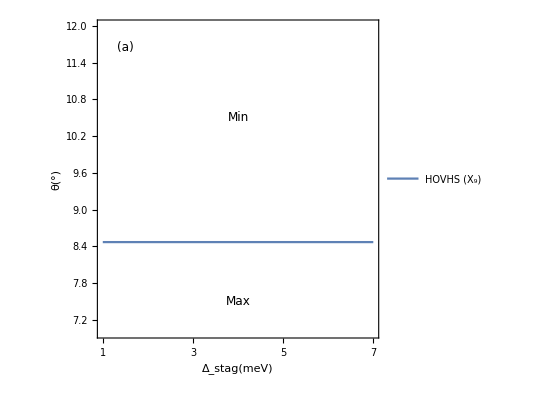

```mathematica
FitFunc3M=Interpolation[HosListBand3M[[All,1;;2]]];
Panel1=Show[(*PlotBand9,*)Plot[FitFunc3M[x/1000],{x,1,7},FrameLabel->{"Δ_stag(meV)","θ(°)"},PlotLegends->Placed[{Style["HOVHS (X_9)",FontFamily->"Arial",FontSize->10]},{0.6,0.92}],PlotRange->{{1,7},{7,12}},Frame->True,AspectRatio->1,FrameTicks->{{Automatic,None},{{1,3,5,7},None}}],Graphics[Text[Style["Max",FontFamily->"Arial",FontSize->12],{4,7.5}]],Graphics[Text[Style["Min",FontFamily->"Arial",FontSize->12],{4,10.5}]],Graphics[Text[Style["(a)",FontFamily->"Arial",FontSize->12],{1.5,11.65}]]]
```

### Band 4

```mathematica
HosListBand4M={};
SetSharedVariable[HosListBand4M];

ParallelDo[
HamCurr[k_]:=Hamltn1[k[[1]]-k[[2]],k[[1]]+k[[2]],k[[3]],Delt];

θCurr=8.46;
CurrResln=10^-3;
HOSFound=False;
NoTry=1;

While[NoTry<=4&&HOSFound==False,
TaylorPoly=Chop[TaylorExpandBand[HamCurr(*The Hamiltonian*),{0,π//N,θCurr}(*the (k,t) point at which we are going to series expand.*),4(*Band to series expand*),2(*Degree of Taylor polynomial*),"Dimension"->2(*k-space dimension*),"TuningDegree"->2(*Degree of tuning parameter terms*),"TuningSymbol"->"δθ"(*Symbols for the tuning parameters*),"Resolution"->10^-4(*Resolution below which we shall kill terms*),"SampleDirection"->{0.333,0.779,0.1335}(*A sample k-vector that will be used for diagonalising symbolic matrices. This is not needed in principle since we will generate a random one in the routine if this is not provided*),"Messages"->False(*YesMessage*)],10^-6];

HesDet=(D[TaylorPoly[[1,3]],{p1,2}]D[TaylorPoly[[1,3]],{p2,2}]-(D[TaylorPoly[[1,3]],p1,p2])^2)/.{p1->0,p2->0}//Simplify;

If[Chop[ReplaceAll[HesDet,{δθ->0}],CurrResln]==0,
HOSFound=True;
];

δθSolns=Solve[HesDet==0,δθ,Reals];

MinSoln=1;
Do[
If[Abs[ReplaceAll[δθ,δθSolns[[l]]]]<Abs[ReplaceAll[δθ,δθSolns[[MinSoln]]]],
MinSoln=l;
]
,{l,1,Length[δθSolns]}];

θCurr=θCurr+δθ/.δθSolns[[MinSoln]];
];

If[HOSFound==True,
TaylorPoly=Chop[TaylorExpandBand[HamCurr(*The Hamiltonian*),{0,π//N,θCurr}(*the (k,t) point at which we are going to series expand.*),4(*Band to series expand*),4(*Degree of Taylor polynomial*),"Dimension"->2(*k-space dimension*),"TuningDegree"->0(*Degree of tuning parameter terms*),"TuningSymbol"->"δθ"(*Symbols for the tuning parameters*),"Resolution"->10^-4(*Resolution below which we shall kill terms*),"SampleDirection"->{0.333,0.779,0.1335}(*A sample k-vector that will be used for diagonalising symbolic matrices. This is not needed in principle since we will generate a random one in the routine if this is not provided*),"Messages"->False(*YesMessage*)],10^-6];

AppendTo[HosListBand4M,{Delt,θCurr,NoTry,Total[Chop[ReplaceAll[TaylorPoly[[1]],{p1->Subscript[k, x],p2->Subscript[k, y],δθ->0}],CurrResln]]}];
,
Print[Style["No HOS found in the range!",Red]];
];

,{Delt,0.001,0.008,0.001}]
```

We will have to sort the list since it was constructed using a parallelized Do loop:

```mathematica
HosListBand4M=SortBy[HosListBand4M,First];
```

Using this, we can diagnose the HOS and view the θ_crit and Taylor expansion for each Δ:

```mathematica
Do[
Print["Δ_stag = ",Round[1000hosdata[[1]]],"meV. Search converged after ",hosdata[[3]]," iterations."];
Print["\t"<>"θ_crit = ",NumberForm[hosdata[[2]],{4,2}],", Tayl = ",NumberForm[hosdata[[4]],{4,3}]];
DiagnoseHOS[Chop[hosdata[[4]],10^-2]];
Print["********************************************************************"]

,{hosdata,HosListBand4M}]
```

Δ_stag = 1meV. Search converged after 1 iterations.

θ_crit = 8.47, Tayl = -0.080+1.866 k_x^4-0.103 k_x^3 k_y-4.133 k_x^2 k_y^2+0.103 k_x k_y^3+1.866 k_y^4

Polynomial has corank 2. It is 5-determinate. Its determinacy is either 5 or 4 and its codimension is 8. Comparing with the known list of singularities:

Polynomial has a catastrophe belonging to the X_9 singularity class.

********************************************************************

Δ_stag = 2meV. Search converged after 1 iterations.

θ_crit = 8.47, Tayl = -0.079+0.826 k_x^4-0.103 k_x^3 k_y-2.053 k_x^2 k_y^2+0.103 k_x k_y^3+0.826 k_y^4

Polynomial has corank 2. It is 5-determinate. Its determinacy is either 5 or 4 and its codimension is 8. Comparing with the known list of singularities:

Polynomial has a catastrophe belonging to the X_9 singularity class.

********************************************************************

Δ_stag = 3meV. Search converged after 1 iterations.

θ_crit = 8.47, Tayl = -0.078+0.479 k_x^4-0.103 k_x^3 k_y-1.359 k_x^2 k_y^2+0.103 k_x k_y^3+0.479 k_y^4

Polynomial has corank 2. It is 5-determinate. Its determinacy is either 5 or 4 and its codimension is 8. Comparing with the known list of singularities:

Polynomial has a catastrophe belonging to the X_9 singularity class.

********************************************************************

Δ_stag = 4meV. Search converged after 1 iterations.

θ_crit = 8.47, Tayl = -0.077+0.305 k_x^4-0.103 k_x^3 k_y-1.012 k_x^2 k_y^2+0.103 k_x k_y^3+0.305 k_y^4

Polynomial has corank 2. It is 5-determinate. Its determinacy is either 5 or 4 and its codimension is 8. Comparing with the known list of singularities:

Polynomial has a catastrophe belonging to the X_9 singularity class.

********************************************************************

Δ_stag = 5meV. Search converged after 1 iterations.

θ_crit = 8.47, Tayl = -0.076+0.201 k_x^4-0.103 k_x^3 k_y-0.804 k_x^2 k_y^2+0.103 k_x k_y^3+0.201 k_y^4

Polynomial has corank 2. It is 5-determinate. Its determinacy is either 5 or 4 and its codimension is 8. Comparing with the known list of singularities:

Polynomial has a catastrophe belonging to the X_9 singularity class.

********************************************************************

Δ_stag = 6meV. Search converged after 1 iterations.

θ_crit = 8.47, Tayl = -0.075+0.132 k_x^4-0.103 k_x^3 k_y-0.665 k_x^2 k_y^2+0.103 k_x k_y^3+0.132 k_y^4

Polynomial has corank 2. It is 5-determinate. Its determinacy is either 5 or 4 and its codimension is 8. Comparing with the known list of singularities:

Polynomial has a catastrophe belonging to the X_9 singularity class.

********************************************************************

Δ_stag = 7meV. Search converged after 1 iterations.

θ_crit = 8.47, Tayl = -0.074+0.082 k_x^4-0.103 k_x^3 k_y-0.566 k_x^2 k_y^2+0.103 k_x k_y^3+0.082 k_y^4

Polynomial has corank 2. It is 5-determinate. Its determinacy is either 5 or 4 and its codimension is 8. Comparing with the known list of singularities:

Polynomial has a catastrophe belonging to the X_9 singularity class.

********************************************************************

Δ_stag = 8meV. Search converged after 1 iterations.

θ_crit = 8.47, Tayl = -0.073+0.045 k_x^4-0.103 k_x^3 k_y-0.492 k_x^2 k_y^2+0.103 k_x k_y^3+0.045 k_y^4

Polynomial has corank 2. It is 5-determinate. Its determinacy is either 5 or 4 and its codimension is 8. Comparing with the known list of singularities:

Polynomial has a catastrophe belonging to the X_9 singularity class.

********************************************************************

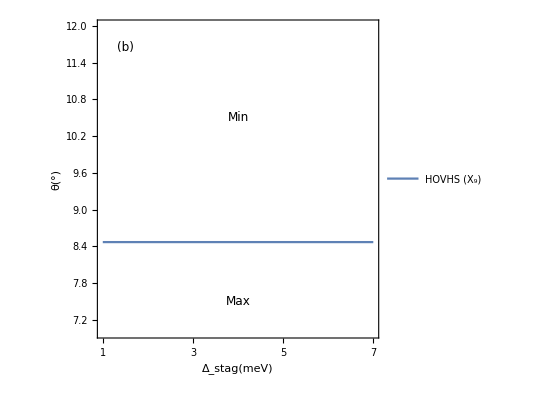

```mathematica
FitFunc4M=Interpolation[HosListBand4M[[All,1;;2]]];
Panel2=Show[(*PlotBand9,*)Plot[FitFunc4M[x/1000],{x,1,7},FrameLabel->{"Δ_stag(meV)","θ(°)"},PlotLegends->Placed[{Style["HOVHS (X_9)",FontFamily->"Arial",FontSize->10]},{0.6,0.92}],PlotRange->{{1,7},{7,12}},Frame->True,AspectRatio->1,FrameTicks->{{Automatic,None},{{1,3,5,7},None}}],Graphics[Text[Style["Max",FontFamily->"Arial",FontSize->12],{4,7.5}]],Graphics[Text[Style["Min",FontFamily->"Arial",FontSize->12],{4,10.5}]],Graphics[Text[Style["(b)",FontFamily->"Arial",FontSize->12],{1.5,11.65}]]]
```

## Phase Diagram

```mathematica
θmin=7;
θmax=12(*9.6*);

cm=72/2.54;

TicsFontSize=6;
AxesFontSize=8;
RegionFontColour=LightGray;
FigLength=3.5cm;
LeftPadding=0.5cm;
RightPadding=0.2cm;
BottomPadding=0.5cm;
TopPadding=0.15cm;
xTicsLabeled={{7,"7"},{8,"8"},{9,"9"},{10,"10"},{11,"11"},{12,"12"}};
xTics={7,8,9,10,11,12};
yTics={1,3,5,7};

VHsColour={((*125*)161)/255,((*9*)93)/255,((*184*)216)/255,1(*0.65*)};
MinColour={((*9*)59)/255,((*73*)96)/255,((*184*)196)/255,1(*0.65*)};
MaxColour={((*207*)242)/255,((*17*)70)/255,((*51*)70)/255,1(*0.65*)};

PanA=ParametricPlot[{{v FitFunc4M[u/1000]+θmin(1-v),u},{(1-v)FitFunc4M[u/1000]+θmax v,u}},{u,1,7},{v,0,1},PlotRange->{{θmin,θmax},{1,7}},Frame->True,PlotStyle->{RGBColor[MaxColour],RGBColor[MinColour]},AspectRatio->1,(*FrameTicks->{True,True},*)(*FrameLabel->{None,Style["Δ_nem (%)",FontFamily->"Arial",FontSize->AxesFontSize,FontColor->Black]},*)FrameTicksStyle->{{Directive[Black,FontFamily->"Arial",TicsFontSize],Directive[Black,FontOpacity->0,FontSize->0]},{Directive[Black,FontOpacity->0,FontSize->0],Directive[Black,FontOpacity->0,FontSize->0]}},FrameTicks->{{yTics,yTics},{xTics,xTics}},ImagePadding->{{LeftPadding,RightPadding},{0.6TopPadding,TopPadding}},ImageSize->FigLength];

PanAp2=ParametricPlot[{FitFunc4M[u/1000],u},{u,1,7},Axes->False,Frame->False,PlotStyle->{Black,Thickness[0.018]},PlotRange->{{θmin,θmax},{1,7}},PlotLegends->Placed[LineLegend[{Style["X_9",FontFamily->"Arial",FontSize->TicsFontSize,FontColor->RegionFontColour]},LegendMarkerSize->{10,1.3}],{{0.75,0.92},{0.5,0.5}}]];

FullTopPan=Labeled[Show[PanA,PanAp2,Graphics[Rotate[Text[Style["Maximum",FontFamily->"Arial",FontColor->RegionFontColour,FontSize->TicsFontSize],{7.75,4}],90Degree]],Graphics[Text[Style["Minimum",FontFamily->"Arial",FontColor->RegionFontColour,FontSize->TicsFontSize],{10.5,4}]]],{Style["Δ_st (meV)",FontFamily->"Arial",FontSize->AxesFontSize,FontColor->Black],""},{Left,Bottom},Spacings->{0, 0},RotateLabel->True]


PanB=ParametricPlot[{{v FitFunc3M[u/1000]+θmin(1-v),u},{(1-v)FitFunc3M[u/1000]+θmax v,u}},{u,1,7},{v,0,1},PlotRange->{{θmin,θmax},{1,7}},Frame->True,PlotStyle->{RGBColor[MaxColour],RGBColor[MinColour]},AspectRatio->1,FrameTicksStyle->{{Directive[Black,FontFamily->"Arial",TicsFontSize],Directive[Black,FontOpacity->0,FontSize->0]},{Directive[Black,FontFamily->"Arial",TicsFontSize],Directive[Black,FontOpacity->0,FontSize->0]}},FrameTicks->{{yTics,yTics},{xTicsLabeled,xTics}},ImagePadding->{{LeftPadding,RightPadding},{BottomPadding,0.6TopPadding}},ImageSize->FigLength];

PanBp2=ParametricPlot[{FitFunc3M[u/1000],u},{u,1,7},Axes->False,Frame->False,PlotStyle->{Black,Thickness[0.018]},PlotLegends->Placed[LineLegend[{Style["X_9",FontFamily->"Arial",FontSize->TicsFontSize,FontColor->RegionFontColour]},LegendMarkerSize->{10,1.3}],{{0.75,0.92},{0.5,0.5}}]];

FullBottomPan=Labeled[Show[PanB,PanBp2,Graphics[Rotate[Text[Style["Maximum",FontFamily->"Arial",FontColor->RegionFontColour,FontSize->TicsFontSize],{7.75,4}],90Degree]],Graphics[Text[Style["Minimum",FontFamily->"Arial",FontColor->RegionFontColour,FontSize->TicsFontSize],{10.5,4}]]],{Style["Δ_st (meV)",FontFamily->"Arial",FontSize->AxesFontSize,FontColor->Black],Style["θ (°)",FontFamily->"Arial",FontSize->AxesFontSize,FontColor->Black]},{Left,Bottom},Spacings->{0, 0},RotateLabel->True]
```

-Graphics-Δ_st (meV)

-Graphics-Δ_st (meV)θ (°)

These can be labeled and assembled together into final form suitable for publications

```mathematica
GraphicsGrid[{{FullTopPan},{FullBottomPan}},Spacings->{0,-8}]
```

-Graphics-

We will generate the band structure for θ=6°, θ_crit and θ=10°.

```mathematica
Ham1[k_]:=Hamltn1[k[[1]]-k[[2]],k[[1]]+k[[2]],6,0.005]
Bnds1=GenerateBandStructure[Ham1,HSymmPts,"OrbitalProjection"->False,"TotalPoints"->200];
```

```mathematica
plt1=PlotBandStructure[Bnds1,(*{-0.042,0.012}*){-0.2,0.1},AspectRatio->2,"yLabel"->{(*Label*)"E (eV)",(*Font Size*)AxesFontSize,(*Font Color*)Black,(*Font Family*)"Arial"},"xLabel"->{AxesFontSize,Black,"Arial"},"yTicks"->{TicsFontSize,Black,"Helvetica"},"LineThickness"->0.009,"LineColorScheme"->{LightRed},(*Dividing Lines*)"DividingLines"->{(*Dashing[..]*)0.01,(*Color*)Gray,(*Thickness*)0.004},"PlotKeyLegend"->{{Style["θ = 6°",FontSize->TicsFontSize]},{0.25,0.95}}];
```

```mathematica
Ham2[k_]:=Hamltn1[k[[1]]-k[[2]],k[[1]]+k[[2]],θcrit,0.005]
Bnds2=GenerateBandStructure[Ham2,HSymmPts,"OrbitalProjection"->False,"TotalPoints"->400];
```

```mathematica
plt2=PlotBandStructure[Bnds2,(*{-0.042,0.012}*){-0.2,0.1},AspectRatio->2,"yLabel"->{(*Label*)"E (eV)",(*Font Size*)AxesFontSize,(*Font Color*)Black,(*Font Family*)"Arial"},"xLabel"->{AxesFontSize,Black,"Arial"},"yTicks"->{TicsFontSize,Black,"Helvetica"},"LineThickness"->0.009,"LineColorScheme"->{Brown},(*Dividing Lines*)"DividingLines"->{(*Dashing[..]*)0.01,(*Color*)Gray,(*Thickness*)0.004},"PlotKeyLegend"->{{Style["θ = 8.47°",FontSize->TicsFontSize]},{0.25,0.9}}];
```

```mathematica
Ham3[k_]:=Hamltn1[k[[1]]-k[[2]],k[[1]]+k[[2]],10,0.005]
Bnds3=GenerateBandStructure[HamOther2,HSymmPts,"OrbitalProjection"->False,"TotalPoints"->200];
```

```mathematica
plt3=PlotBandStructure[Bnds3,(*{-0.042,0.012}*){-0.2,0.1},AspectRatio->2,"yLabel"->{(*Label*)"E (eV)",(*Font Size*)AxesFontSize,(*Font Color*)Black,(*Font Family*)"Arial"},"xLabel"->{AxesFontSize,Black,"Arial"},"yTicks"->{TicsFontSize,Black,"Helvetica"},"LineThickness"->0.009,"LineColorScheme"->{LightBlue},(*Dividing Lines*)"DividingLines"->{(*Dashing[..]*)0.01,(*Color*)Gray,(*Thickness*)0.004},"PlotKeyLegend"->{{Style["θ = 10°",FontSize->TicsFontSize]},{0.25,0.85}}];
```

```mathematica
BandsFinal=Show[plt1,plt3,plt2,ImageSize->4.5cm]
```

-Graphics-